ⅇ^-λ π μ BesselI[0,λ]

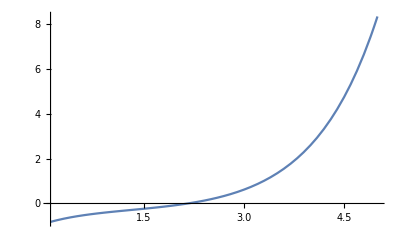

```mathematica
(*Integrate[sgPolar[θ,λ,μ],{θ,0,π/2},Assumptions->λ>0&&μ>0];
Integrate[sgVector[v,{p,λ,μ}],v,Assumptions->λ>0&&μ>0];

sols=Solve[{2^x==4,x>0},x,Reals];*)

(*Reduce[sgPolar[θ,λ,μ]>ϵ && 0≤θ≤π && λ>0 && μ>ϵ && ϵ>0,θ,Reals]*)

(*aaa[μ_,λ_]=Integrate[μ*Exp[λ*(Cos[θ]-1)],{θ,0,π}];*)

aaa=Integrate[μ*Exp[λ*(Cos[θ]-1)],{θ,0,π}]
sgIntegral[λ,μ]/(ⅇ^-λ π^2 μ);
Plot[{BesselI[0,λ]-(2  (ⅇ^λ-ⅇ^(-2λ)))/(π λ)},{λ,0.1,5}]
```

>Warp Rectangle:

1

3

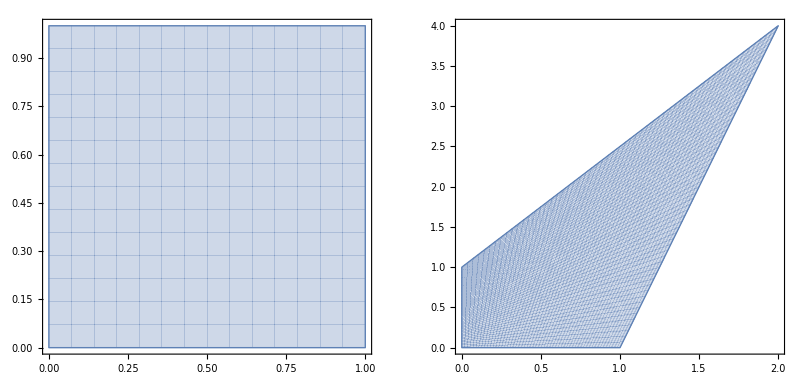

```mathematica
(*https://web.ma.utexas.edu/users/m408s/m408d/CurrentWeb/LM15-10-4.php*)
(*https://math.stackexchange.com/questions/14952/what-is-the-jacobian-matrix*)

x[u_,v_]:=u(1+v);
y[u_,v_]:=v(1+3u);

OriginR=Polygon[{{0,0},{0,1},{1,1},{1,0}}];
WarpR=Polygon[{{x[0,0],y[0,0]},{x[0,1],y[0,1]},{x[1,1],y[1,1]},{x[1,0],y[1,0]}}];
Print[">Warp Rectangle:"  ];
Area[OriginR]
Area[WarpR]
{ParametricPlot[{u,v},{u,0,1},{v,0,1}],ParametricPlot[{x[u,v],y[u,v]},{u,0,1},{v,0,1}]}//GraphicsRow
```

```mathematica
dxu=D[x[u,v],u];
dxv=D[x[u,v],v];
dyu=D[y[u,v],u];
dyv=D[y[u,v],v];
jmat={{dxu,dxv},{dyu,dyv}};

Print[">Jacobian Matrix Det:" Det[jmat]];
jmat//MatrixForm
```

>Jacobian Matrix Det: (1+3 u+v)

(1+v | u
3 v | 1+3 u)

```mathematica
Jaco2=D[{x[u,v],y[u,v]},{{u,v}}]//MatrixForm
```

(1+v | u
3 v | 1+3 u)